# Line integral in ℝ^2

## Field

```mathematica
F[{x_, y_}]={-x+y,-x-y};
(*F[{x_, y_}]={1,2}*)
```

## Line segment

```mathematica
LineSegment={{2,0},{0,2}};
```

## Show

```mathematica
a=2;
```

```mathematica
field=VectorPlot[F[{x, y}],{x,-1.2a,1.2a},{y,-1.2a,1.2a},
FrameLabel->{x,y},
VectorPoints->10,
VectorStyle->Arrowheads[0.03]];
```

```mathematica
line=Graphics[{Red,Thickness[0.01],Arrow[LineSegment]}];
```

```mathematica
xAxis=Graphics[{Text["x",{1.3a,0}],Thickness[0.01],Arrow[{{-1.2a,0},{1.2a,0}}]}];
```

```mathematica
yAxis=Graphics[{Text["y",{0,1.3a}],Thickness[0.01],Arrow[{{0,-1.2a},{0,1.2a}}]}];
```

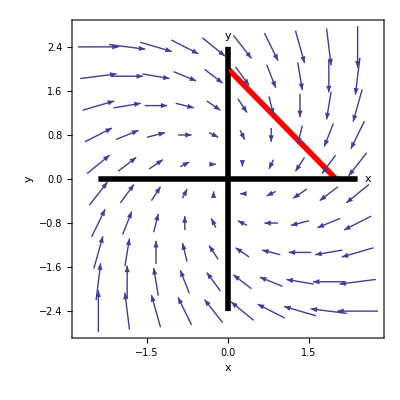

```mathematica
Show[field,line,xAxis,yAxis]
```

## Parametrization for the line segment

```mathematica
r[t_]=LineSegment[[1]](1-t)+LineSegment[[2]]t
```

{2 (1-t),2 t}

## Integral

```mathematica
NIntegrate[F[r[t]].r'[t],{t,0,1}]
```

-4.